```mathematica
(*Import data from the specified file*)dataset=Import["/Users/humayrajeba/Documents/Wolfram Mathematica/THzBlock/Set3_H=135cm_L13=450cm_L12=300cm/DATA_UNCAL_Meas23"];
```

```mathematica
(*Define parameters for processing*)
avgParam=20;
percentage=5;
{time,signal}={dataset[[1;;,1]],dataset[[1;;,2]]};
```

```mathematica
signal
```

```mathematica
signal
```

```mathematica
signal
```

```mathematica
(*Calculate the weighted signal and its exponential moving average*)
weightedSignal=10*Log10[signal]
```

```mathematica
decayRate=0.005;
movingAvg=Re[ExponentialMovingAverage[weightedSignal,decayRate]]
```

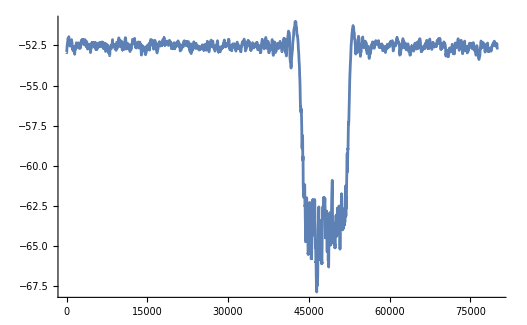

```mathematica
ListLinePlot[movingAvg,PlotRange->All]
```

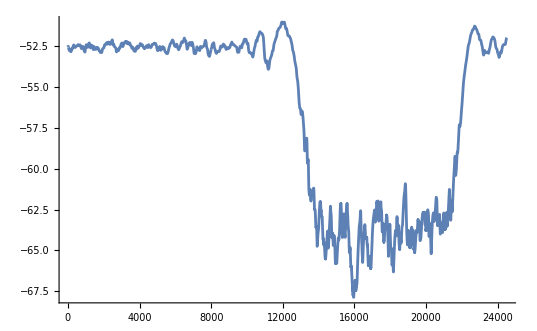

```mathematica
ListLinePlot@Take[movingAvg,{30500,55000}]
```

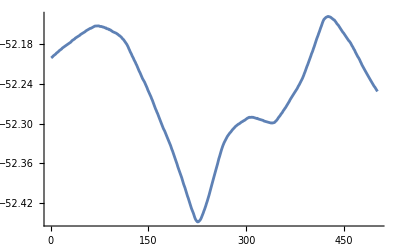

```mathematica
ListLinePlot@Take[movingAvg,{3000,3500}]
```

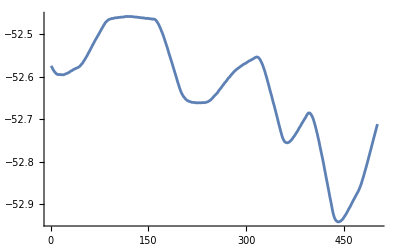

```mathematica
ListLinePlot@Take[movingAvg,{4000,4500}]
```

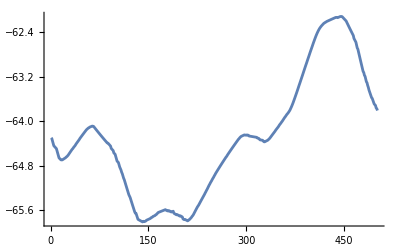

```mathematica
ListLinePlot@Take[movingAvg,{45300,45800}]
```

```mathematica
nonBlocked=Take[movingAvg,{3000,3500}];
oscillating=Take[movingAvg,{4000,4500}];
blocked=Take[movingAvg,{45300,45800}];
```

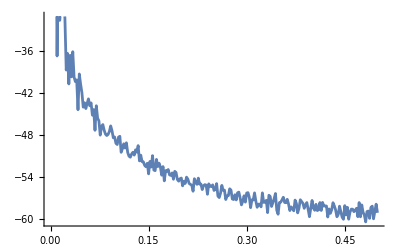

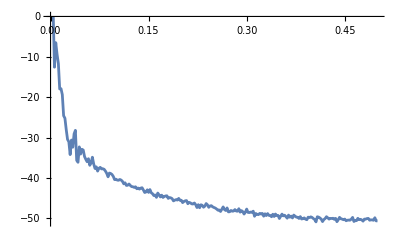

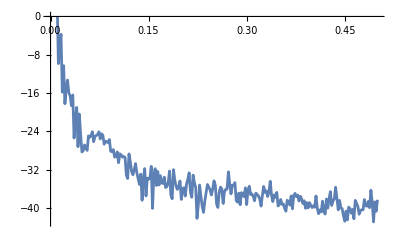

```mathematica
periodogramNonBlocked=Periodogram[nonBlocked,PlotStyle->DarkRed]
periodogramOscillating=Periodogram[oscillating,PlotStyle->DarkMagenta]
periodogramBlocked=Periodogram[blocked,PlotStyle->DarkGreen]
```

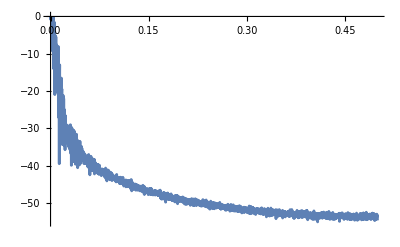

-Graphics-

```mathematica
powerSpectrumNonBlocked=PeriodogramArray[nonBlocked];
powerSpectrumOscillating=PeriodogramArray[oscillating];
powerSpectrumBlocked=PeriodogramArray[blocked];
```

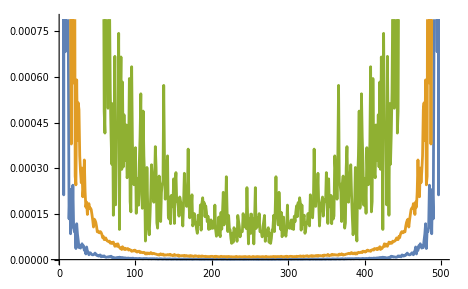

```mathematica
ListLinePlot[{powerSpectrumNonBlocked,powerSpectrumOscillating,powerSpectrumBlocked}]
```

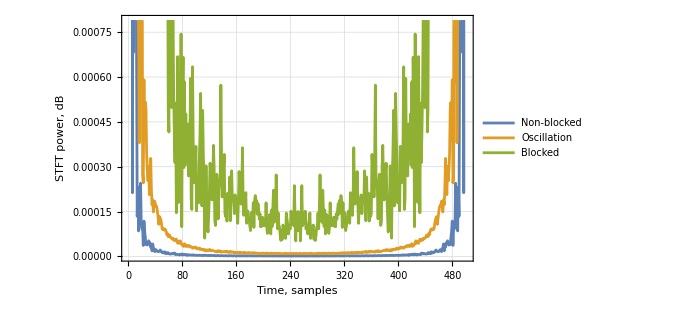

```mathematica
ListLinePlot[{powerSpectrumNonBlocked,powerSpectrumOscillating,powerSpectrumBlocked},GridLines->Automatic,LabelStyle->{FontSize->13,FontFamily->"Times New Roman"},Frame->True,FrameLabel->{Style["Time, samples",Black,15],Style["STFT power, dB",Black,15]},PlotLegends->Placed[LineLegend[{"Non-blocked","Oscillation","Blocked"},LegendFunction->(Framed[#,FrameMargins->0,Background->White,FrameStyle->Lighter[Gray]]&),LabelStyle->Directive[FontSize->13],LegendMargins->5,Spacings->0.35],{0.5,0.7}],ImageSize->500]
```